# The solid-state diode - Experiment 13

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

Note: The plot labels write the current units as A, but the data is in mA and the processing is done with this kept in mind. The plot labels have not been modified because this was noticed after all plots were completed and CurveFit does not save intermediary datasets, so recreating the plots would have been prohibitively time-consuming.

## Testing the PN junction theory

We fit our data for the IV-curves of our diodes at room temperature and dry ice temperature to test how closely the data follows the theory presented in the lab manual. We also fit several regions of each dataset to test the theory in different regimes.

```mathematica
(* We start by writing a function that commits the fit parameters for each region of each dataset to a list with structure {region, a, siga, b, sigb, (χ̃)^2}. Region and (χ̃)^2 have to be entered manually, looking through CurveFit code, documentation and variables does not show (χ̃)^2 being stored as a variable. *)

(* Initializing list *)
fitParam={};
```

```mathematica
(* Commiting fit parameters to list. *)
commitFit[region_,chisq_]:=AppendTo[fitParam,{region,a,siga,b,sigb,chisq}];
```

```mathematica
SetDirectory[StringJoin[NotebookDirectory[],"Diode"]];
```

### Silicon diode - Room Temperature

#### Whole dataset (bad points removed)

For all datasets we remove the lowest data point both for the high-current and low-current data. In lab we observed a discrepancy between measurements at the same current when the measurement corresponded to the lowest-current data point of both the high- and low- current datasets. There was no such discrepancy when the same measurement was not the lowest-current point on a dataset, indicating a hardware issue. Therefore we disregard both those points in the following analysis.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_rt_calibrated.dat

File comment header:

Silicon RTP calibrated
IV Data Set #00139	3:57:07 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17}
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

{Null,Null,Null,Null}

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-0.0154283,0.755987}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0000127106 | b= 
18.347 | 
σ_a= 
9.07978×10^-7 | σ_b= 
0.0958677 | Std. deviation= 
0.0345834

Fit of (x±σ_x,y±σ_y)

a= 
4.35498×10^-6 | b= 
19.927 | 
σ_a= 
4.65343×10^-9 | σ_b= 
0.00180498 | χ^2/(n-2)= 
512.572

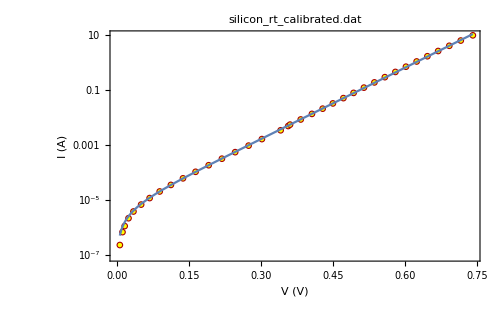
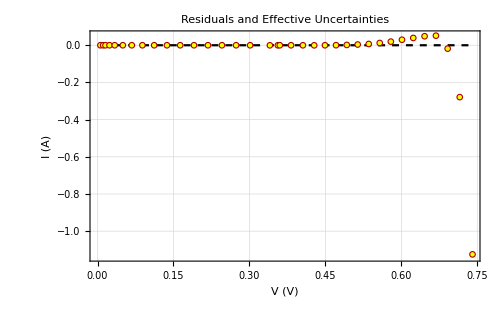
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
4.35498×10^-6 | b= 
19.927 | 
σ_a= 
4.65343×10^-9 | σ_b= 
0.00180498 | χ^2/(n-2)= 
512.572

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{-0.015428312500000001,0.7559873125},512.5724700933897];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_rt_calibrated.dat

File comment header:

Silicon RTP calibrated
IV Data Set #00139	3:57:07 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-0.0154283,0.1484}

n= 10

26 points removed.

```mathematica
DiodeFit[]
```

n = 10

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
4.03361×10^-6 | b= 
20.544 | 
σ_a= 
1.21429×10^-7 | σ_b= 
0.216402 | Std. deviation= 
2.75033×10^-7

Fit of (x±σ_x,y±σ_y)

a= 
3.55954×10^-6 | b= 
21.5518 | 
σ_a= 
2.24398×10^-8 | σ_b= 
0.0548155 | χ^2/(n-2)= 
170.084

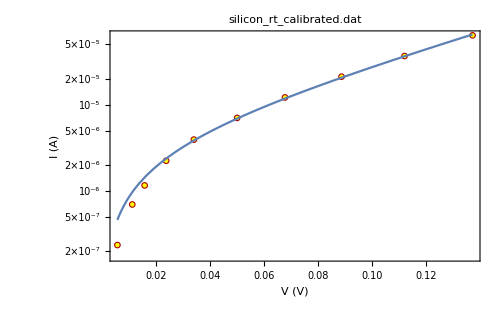
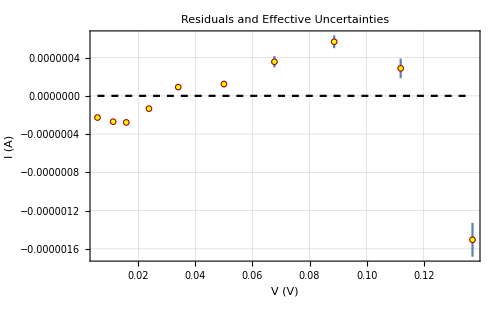
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
3.55954×10^-6 | b= 
21.5518 | 
σ_a= 
2.24398×10^-8 | σ_b= 
0.0548155 | χ^2/(n-2)= 
170.084

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{-0.015428312500000001,0.1484},170.08393446581536];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_rt_calibrated.dat

File comment header:

Silicon RTP calibrated
IV Data Set #00139	3:57:07 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.206,0.5024}

n= 13

23 points removed.

```mathematica
DiodeFit[]
```

n = 13

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
3.53461×10^-6 | b= 
20.3906 | 
σ_a= 
9.19049×10^-8 | σ_b= 
0.0538937 | Std. deviation= 
0.000136034

Fit of (x±σ_x,y±σ_y)

a= 
3.99897×10^-6 | b= 
20.1083 | 
σ_a= 
1.53239×10^-8 | σ_b= 
0.0101499 | χ^2/(n-2)= 
41.4013

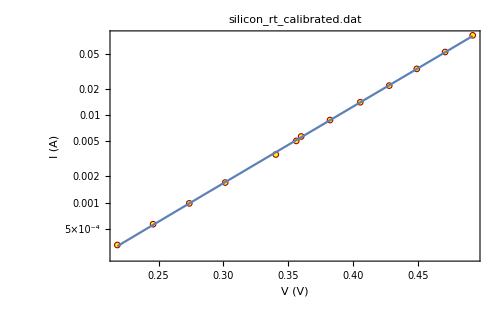
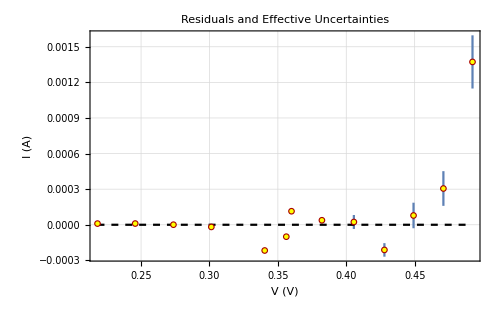
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
3.99897×10^-6 | b= 
20.1083 | 
σ_a= 
1.53239×10^-8 | σ_b= 
0.0101499 | χ^2/(n-2)= 
41.4013

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.20600000000000002,0.5024000000000001},41.401251771117565];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_rt_calibrated.dat

File comment header:

Silicon RTP calibrated
IV Data Set #00139	3:57:07 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.501,0.755987}

n= 11

25 points removed.

```mathematica
DiodeFit[]
```

n = 11

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0000128106 | b= 
18.3362 | 
σ_a= 
1.80722×10^-6 | σ_b= 
0.184309 | Std. deviation= 
0.0659571

Fit of (x±σ_x,y±σ_y)

a= 
6.56404×10^-6 | b= 
19.3088 | 
σ_a= 
2.94935×10^-8 | σ_b= 
0.00677837 | χ^2/(n-2)= 
626.02

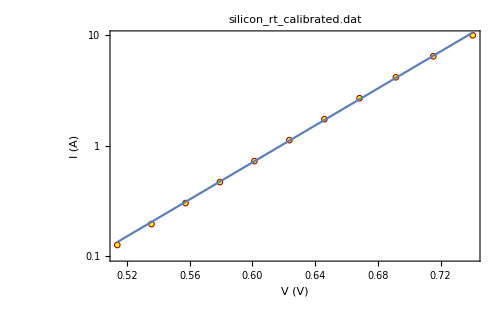
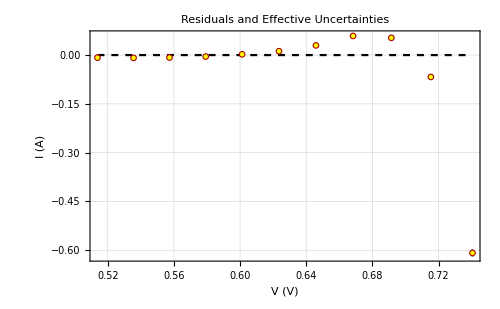
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
6.56404×10^-6 | b= 
19.3088 | 
σ_a= 
2.94935×10^-8 | σ_b= 
0.00677837 | χ^2/(n-2)= 
626.02

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.501,0.7559873125},626.0195037513873];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
siliconRT=fitParam;
```

```mathematica
fitParam={};
```

### Silicon diode - Dry Ice Temperature

#### Whole dataset (bad points removed)

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_di.dat

File comment header:

Silicon Dry Ice calibrated
IV Data Set #00169	4:09:30 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17}
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

{Null,Null,Null,Null}

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.323086,0.911654}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
8.44275×10^-11 | b= 
28.3572 | 
σ_a= 
6.75674×10^-11 | σ_b= 
0.10081 | Std. deviation= 
0.0623512

Fit of (x±σ_x,y±σ_y)

a= 
1.40303×10^-11 | b= 
30.4339 | 
σ_a= 
3.64541×10^-14 | σ_b= 
0.00323305 | χ^2/(n-2)= 
453.09

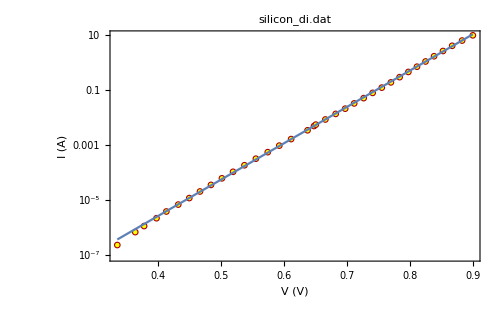
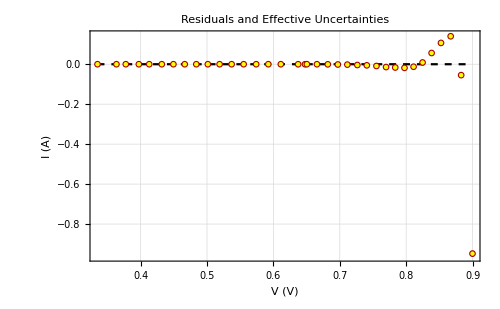
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
1.40303×10^-11 | b= 
30.4339 | 
σ_a= 
3.64541×10^-14 | σ_b= 
0.00323305 | χ^2/(n-2)= 
453.09

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.32308562499999993,0.911654375},453.08954952184655];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_di.dat

File comment header:

Silicon Dry Ice calibrated
IV Data Set #00169	4:09:30 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.323086,0.5102}

n= 10

26 points removed.

```mathematica
DiodeFit[]
```

n = 10

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
7.75498×10^-12 | b= 
31.7468 | 
σ_a= 
3.16701×10^-13 | σ_b= 
0.0731675 | Std. deviation= 
8.89566×10^-8

Fit of (x±σ_x,y±σ_y)

a= 
5.30356×10^-12 | b= 
32.5559 | 
σ_a= 
8.93198×10^-14 | σ_b= 
0.0372247 | χ^2/(n-2)= 
92.7384

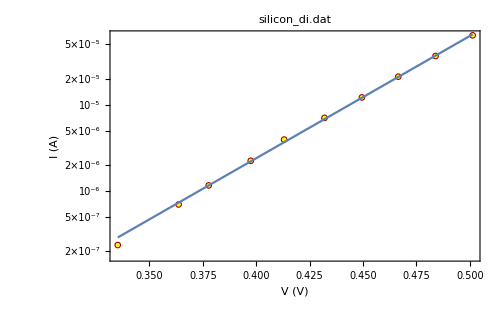
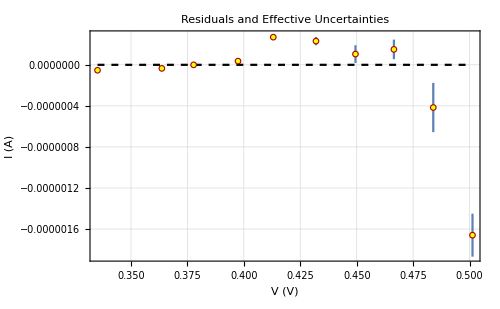
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
5.30356×10^-12 | b= 
32.5559 | 
σ_a= 
8.93198×10^-14 | σ_b= 
0.0372247 | χ^2/(n-2)= 
92.7384

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.32308562499999993,0.5102},92.73844942065703];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_di.dat

File comment header:

Silicon Dry Ice calibrated
IV Data Set #00169	4:09:30 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.5082,0.7202}

n= 13

23 points removed.

```mathematica
DiodeFit[]
```

n = 13

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
2.25637×10^-11 | b= 
29.6831 | 
σ_a= 
2.8921×10^-12 | σ_b= 
0.173143 | Std. deviation= 
0.000126411

Fit of (x±σ_x,y±σ_y)

a= 
2.19361×10^-11 | b= 
29.7281 | 
σ_a= 
2.20064×10^-13 | σ_b= 
0.0158754 | χ^2/(n-2)= 
21.9023

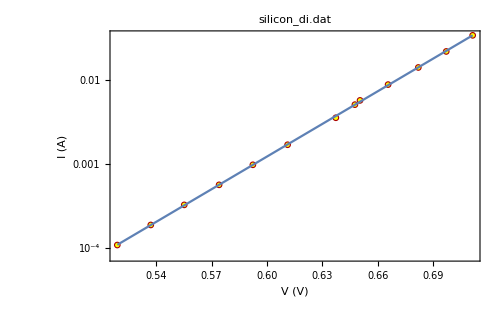
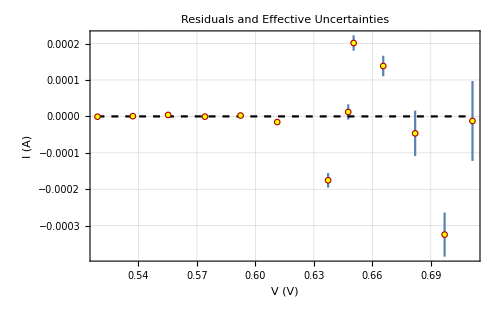
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
2.19361×10^-11 | b= 
29.7281 | 
σ_a= 
2.20064×10^-13 | σ_b= 
0.0158754 | χ^2/(n-2)= 
21.9023

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.5082,0.7202000000000001},21.90234094658127];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/silicon_di.dat

File comment header:

Silicon Dry Ice calibrated
IV Data Set #00169	4:09:30 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.7176,0.911867}

n= 13

27 points removed.

```mathematica
DiodeFit[]
```

n = 13

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
7.84517×10^-11 | b= 
28.4372 | 
σ_a= 
1.054×10^-10 | σ_b= 
0.233385 | Std. deviation= 
0.110971

Fit of (x±σ_x,y±σ_y)

Minimizing Chi^2

a= 
1.19161×10^-11 | b= 
30.625 | 
σ_a= 
1.24639×10^-13 | σ_b= 
0.0122291 | χ^2/(n-2)= 
785.199

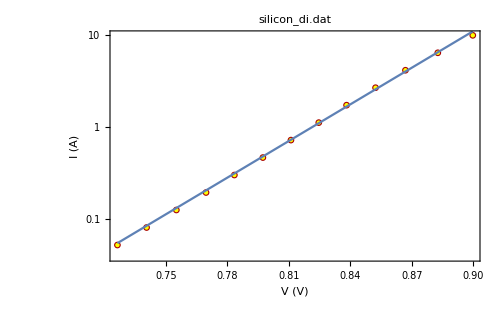
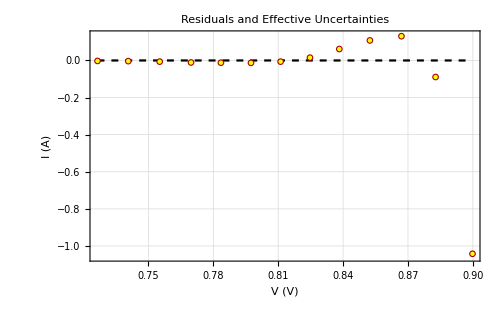
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
1.19161×10^-11 | b= 
30.625 | 
σ_a= 
1.24639×10^-13 | σ_b= 
0.0122291 | χ^2/(n-2)= 
785.199

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.7176,0.9118667291666667},785.1993496718917];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
siliconDI=fitParam;
```

```mathematica
fitParam={};
```

### Germanium diode - Room Temperature

#### Whole dataset (bad points removed)

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_rt_calibrated.dat

File comment header:

Germanium RTP calibrated
IV Data Set #00136	3:51:58 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

LoadFile::sorted: Data sorted in increasing x order.

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17}
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

{Null,Null,Null,Null}

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-0.00877563,0.417906}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.012185 | b= 
16.4377 | 
σ_a= 
0.000858298 | σ_b= 
0.175828 | Std. deviation= 
0.0725066

Fit of (x±σ_x,y±σ_y)

a= 
0.00403687 | b= 
19.5712 | 
σ_a= 
5.81426×10^-6 | σ_b= 
0.00438953 | χ^2/(n-2)= 
10170.8

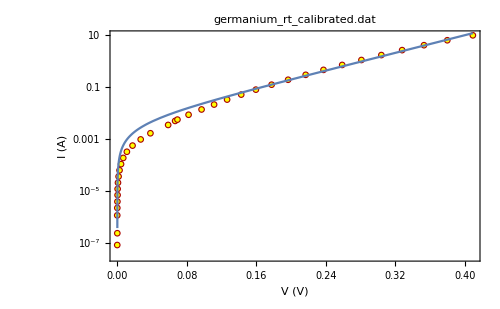
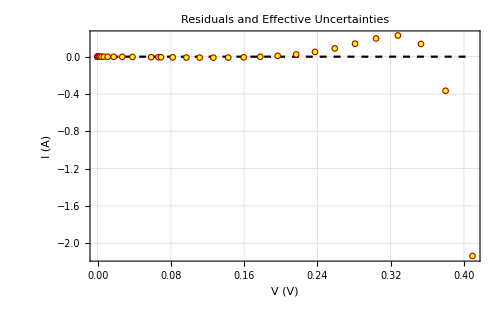
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
0.00403687 | b= 
19.5712 | 
σ_a= 
5.81426×10^-6 | σ_b= 
0.00438953 | χ^2/(n-2)= 
10170.8

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{-0.008775625,0.41790562499999995},10170.77697297076];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_rt_calibrated.dat

File comment header:

Germanium RTP calibrated
IV Data Set #00136	3:51:58 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

LoadFile::sorted: Data sorted in increasing x order.

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-0.00877563,0.0908}

n= 20

16 points removed.

```mathematica
DiodeFit[]
```

n = 20

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.000671112 | b= 
32.1986 | 
σ_a= 
0.0000342683 | σ_b= 
0.61057 | Std. deviation= 
0.0000633357

Fit of (x±σ_x,y±σ_y)

a= 
0.000777601 | b= 
30.326 | 
σ_a= 
7.22748×10^-6 | σ_b= 
0.124108 | χ^2/(n-2)= 
16.2077

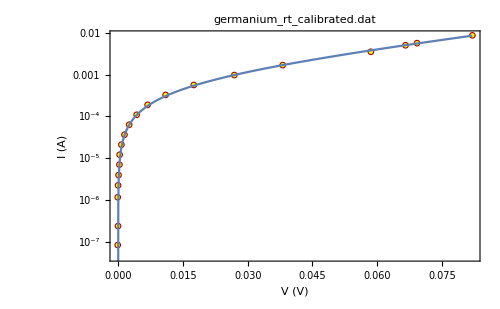
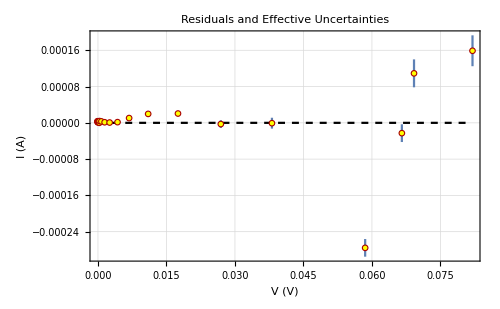
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
0.000777601 | b= 
30.326 | 
σ_a= 
7.22748×10^-6 | σ_b= 
0.124108 | χ^2/(n-2)= 
16.2077

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{-0.008775625,0.0908},16.207728611078206];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_rt_calibrated.dat

File comment header:

Germanium RTP calibrated
IV Data Set #00136	3:51:58 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

LoadFile::sorted: Data sorted in increasing x order.

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.104,0.2466}

n= 8

28 points removed.

```mathematica
DiodeFit[]
```

n = 8

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0025207 | b= 
22.0547 | 
σ_a= 
0.000198186 | σ_b= 
0.33886 | Std. deviation= 
0.00433868

Fit of (x±σ_x,y±σ_y)

a= 
0.00188447 | b= 
23.4242 | 
σ_a= 
7.52439×10^-6 | σ_b= 
0.0209988 | χ^2/(n-2)= 
411.611

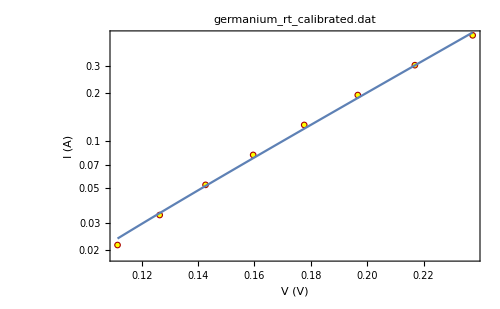
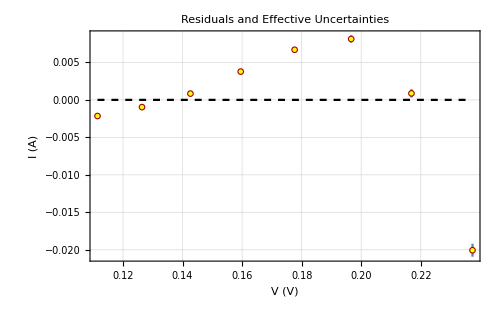
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
0.00188447 | b= 
23.4242 | 
σ_a= 
7.52439×10^-6 | σ_b= 
0.0209988 | χ^2/(n-2)= 
411.611

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.10400000000000001,0.2466},411.61120822450107];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_rt_calibrated.dat

File comment header:

Germanium RTP calibrated
IV Data Set #00136	3:51:58 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

LoadFile::sorted: Data sorted in increasing x order.

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.2473,0.417906}

n= 7

29 points removed.

```mathematica
DiodeFit[]
```

n = 7

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0134021 | b= 
16.1971 | 
σ_a= 
0.00210273 | σ_b= 
0.378707 | Std. deviation= 
0.145723

Fit of (x±σ_x,y±σ_y)

a= 
0.0097824 | b= 
17.0552 | 
σ_a= 
0.0000209918 | σ_b= 
0.00600576 | χ^2/(n-2)= 
4168.84

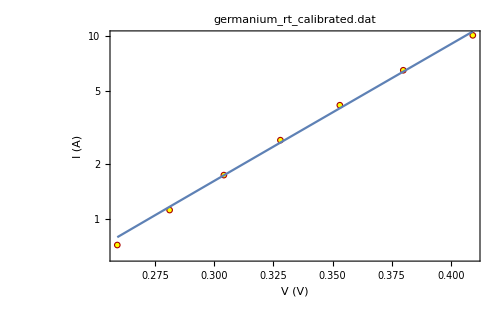
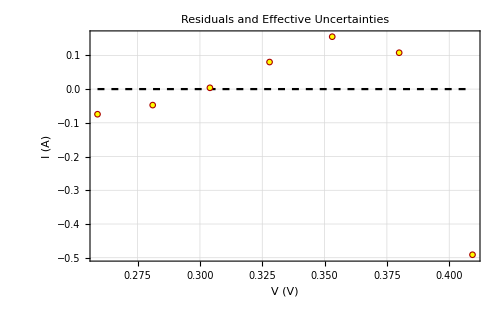
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
0.0097824 | b= 
17.0552 | 
σ_a= 
0.0000209918 | σ_b= 
0.00600576 | χ^2/(n-2)= 
4168.84

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.2473,0.41790562499999995},4168.841482732459];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
germaniumRT=fitParam;
```

```mathematica
fitParam={};
```

### Germanium diode - Dry Ice Temperature

#### Whole dataset (bad points removed)

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_di.dat

File comment header:

Germanium Dry Ice calibrated
IV Data Set #00208	4:20:52 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.0528011,0.564946}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0000619005 | b= 
21.6771 | 
σ_a= 
0.0000160183 | σ_b= 
0.4368 | Std. deviation= 
0.151976

Fit of (x±σ_x,y±σ_y)

a= 
4.75907×10^-7 | b= 
31.5107 | 
σ_a= 
1.21462×10^-9 | σ_b= 
0.00551868 | χ^2/(n-2)= 
43186.9

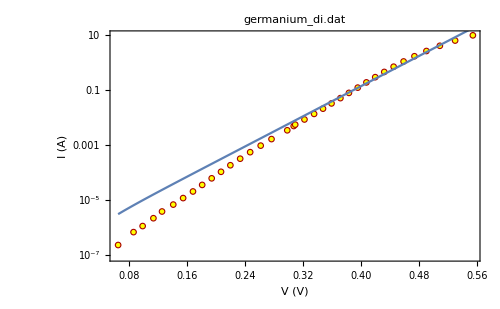
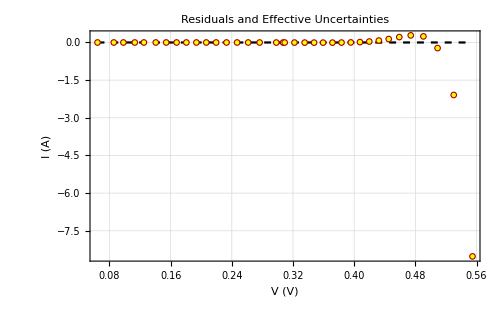
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
4.75907×10^-7 | b= 
31.5107 | 
σ_a= 
1.21462×10^-9 | σ_b= 
0.00551868 | χ^2/(n-2)= 
43186.9

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.05280110416666667,0.5649458958333333},43186.93739403151];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_di.dat

File comment header:

Germanium Dry Ice calibrated
IV Data Set #00208	4:20:52 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.0528011,0.1999}

n= 10

26 points removed.

```mathematica
DiodeFit[]
```

n = 10

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
1.89041×10^-8 | b= 
41.8888 | 
σ_a= 
8.87761×10^-10 | σ_b= 
0.220516 | Std. deviation= 
1.99024×10^-7

Fit of (x±σ_x,y±σ_y)

a= 
2.08452×10^-8 | b= 
41.3377 | 
σ_a= 
5.04666×10^-10 | σ_b= 
0.140402 | χ^2/(n-2)= 
5.28525

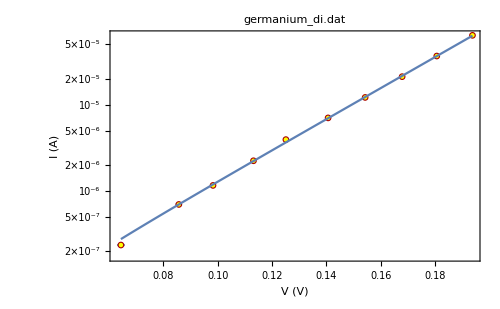
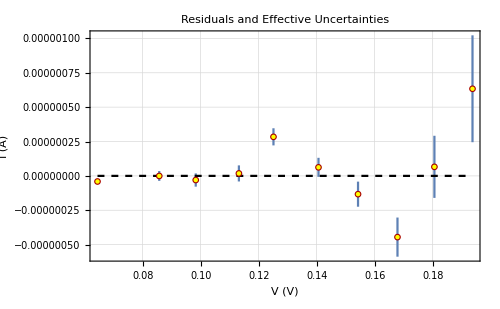
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
2.08452×10^-8 | b= 
41.3377 | 
σ_a= 
5.04666×10^-10 | σ_b= 
0.140402 | χ^2/(n-2)= 
5.28525

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.05280110416666667,0.19990000000000002},5.285252955291375];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_di.dat

File comment header:

Germanium Dry Ice calibrated
IV Data Set #00208	4:20:52 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.2008,0.3901}

n= 15

21 points removed.

```mathematica
DiodeFit[]
```

n = 15

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
6.56754×10^-8 | b= 
36.5739 | 
σ_a= 
2.72016×10^-9 | σ_b= 
0.108556 | Std. deviation= 
0.000152488

Fit of (x±σ_x,y±σ_y)

a= 
6.61959×10^-8 | b= 
36.5684 | 
σ_a= 
3.635×10^-10 | σ_b= 
0.0163476 | χ^2/(n-2)= 
139.803

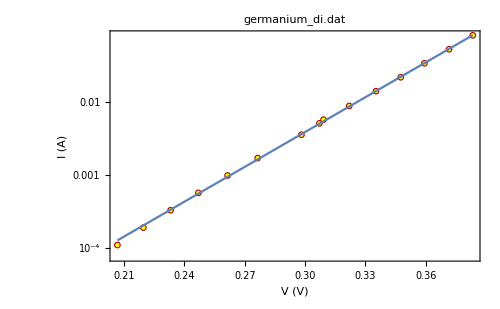
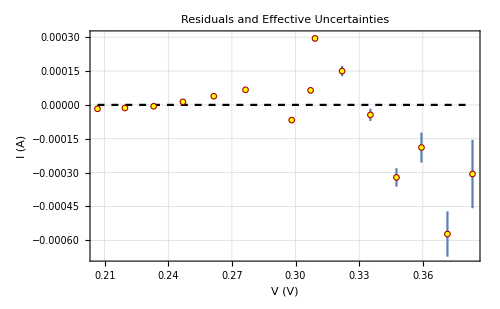
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
6.61959×10^-8 | b= 
36.5684 | 
σ_a= 
3.635×10^-10 | σ_b= 
0.0163476 | χ^2/(n-2)= 
139.803

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.2008,0.3901},139.80254205738402];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/germanium_di.dat

File comment header:

Germanium Dry Ice calibrated
IV Data Set #00208	4:20:52 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.4148,0.564946}

n= 9

27 points removed.

```mathematica
DiodeFit[]
```

n = 9

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
0.0000764766 | b= 
21.288 | 
σ_a= 
0.0000440659 | σ_b= 
0.876951 | Std. deviation= 
0.289559

Fit of (x±σ_x,y±σ_y)

a= 
0.0000108504 | b= 
25.0939 | 
σ_a= 
3.02275×10^-8 | σ_b= 
0.00560288 | χ^2/(n-2)= 
45693.8

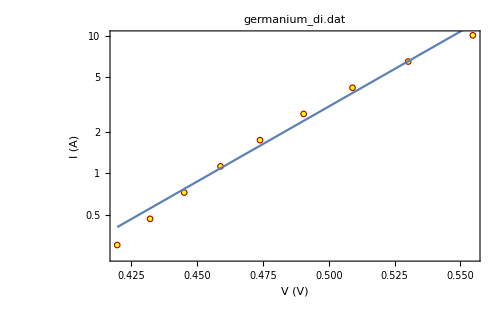
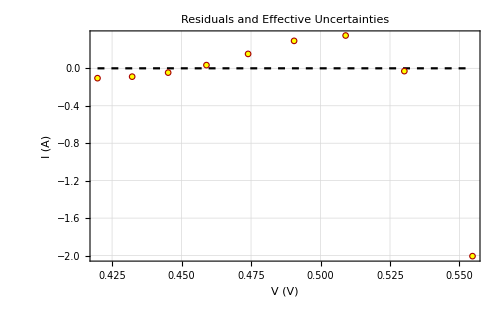
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
0.0000108504 | b= 
25.0939 | 
σ_a= 
3.02275×10^-8 | σ_b= 
0.00560288 | χ^2/(n-2)= 
45693.8

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.4148,0.5649458958333333},45693.79129063999];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
germaniumDI=fitParam;
```

```mathematica
fitParam={};
```

### Transistor - Room Temperature

#### Whole dataset (bad points removed)

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_rt_calibrated.dat

File comment header:

Transistor RTP calibrated
IV Data Set #00142	3:58:53 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.22701,0.693855}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
1.66119×10^-10 | b= 
36.2812 | 
σ_a= 
1.07399×10^-10 | σ_b= 
0.0420632 | Std. deviation= 
0.0318915

Fit of (x±σ_x,y±σ_y)

a= 
3.64202×10^-11 | b= 
38.6257 | 
σ_a= 
1.15854×10^-13 | σ_b= 
0.00530517 | χ^2/(n-2)= 
204.849

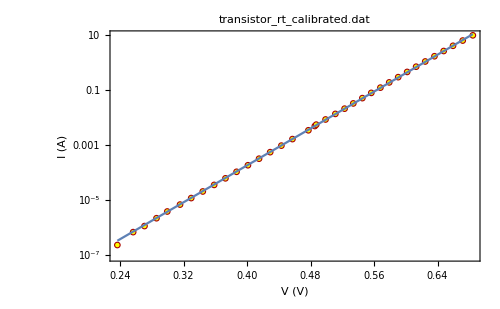
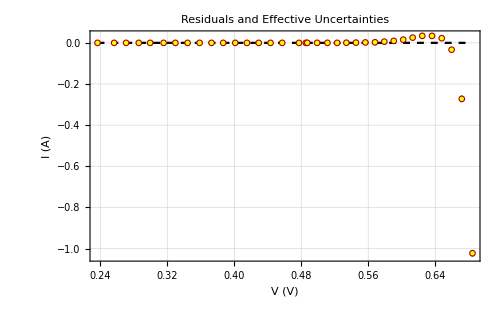
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
3.64202×10^-11 | b= 
38.6257 | 
σ_a= 
1.15854×10^-13 | σ_b= 
0.00530517 | χ^2/(n-2)= 
204.849

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.22701010416666667,0.6938548958333333},204.84853397967123];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_rt_calibrated.dat

File comment header:

Transistor RTP calibrated
IV Data Set #00142	3:58:53 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.22701,0.3649}

n= 9

27 points removed.

```mathematica
DiodeFit[]
```

n = 9

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
4.03606×10^-11 | b= 
38.2434 | 
σ_a= 
2.17307×10^-12 | σ_b= 
0.131534 | Std. deviation= 
7.82992×10^-8

Fit of (x±σ_x,y±σ_y)

a= 
2.78634×10^-11 | b= 
39.3656 | 
σ_a= 
6.63776×10^-13 | σ_b= 
0.0734669 | χ^2/(n-2)= 
86.5428

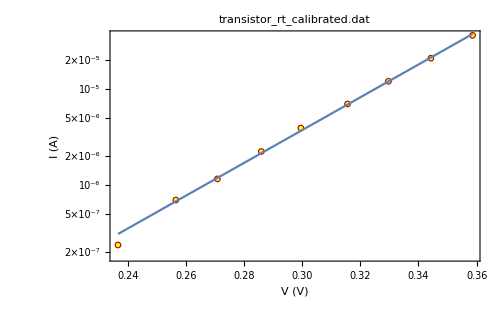
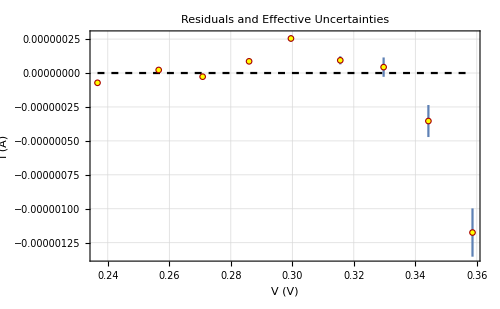
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
2.78634×10^-11 | b= 
39.3656 | 
σ_a= 
6.63776×10^-13 | σ_b= 
0.0734669 | χ^2/(n-2)= 
86.5428

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.22701010416666667,0.3649},86.54277146677468];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_rt_calibrated.dat

File comment header:

Transistor RTP calibrated
IV Data Set #00142	3:58:53 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.3976,0.5514}

n= 13

23 points removed.

```mathematica
DiodeFit[]
```

n = 13

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
3.16557×10^-11 | b= 
38.9223 | 
σ_a= 
2.57571×10^-12 | σ_b= 
0.14619 | Std. deviation= 
0.000126256

Fit of (x±σ_x,y±σ_y)

a= 
3.04044×10^-11 | b= 
38.9992 | 
σ_a= 
4.3288×10^-13 | σ_b= 
0.0291436 | χ^2/(n-2)= 
20.852

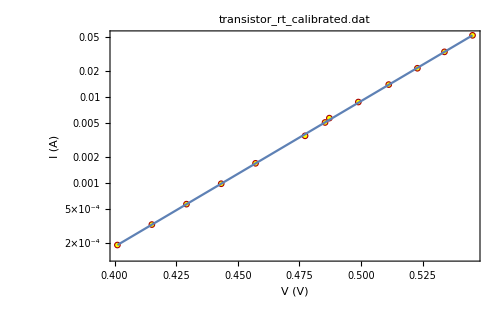
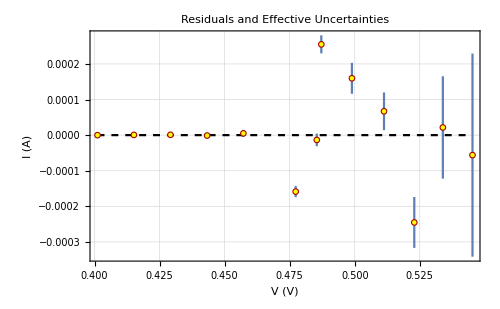
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
3.04044×10^-11 | b= 
38.9992 | 
σ_a= 
4.3288×10^-13 | σ_b= 
0.0291436 | χ^2/(n-2)= 
20.852

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.39760000000000006,0.5514000000000001},20.85201748541172];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_rt_calibrated.dat

File comment header:

Transistor RTP calibrated
IV Data Set #00142	3:58:53 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 10;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.5629,0.693855}

n= 11

25 points removed.

```mathematica
DiodeFit[]
```

n = 11

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
1.99953×10^-10 | b= 
36.005 | 
σ_a= 
6.67425×10^-11 | σ_b= 
0.246669 | Std. deviation= 
0.0576613

Fit of (x±σ_x,y±σ_y)

a= 
7.5261×10^-11 | b= 
37.4882 | 
σ_a= 
8.96097×10^-13 | σ_b= 
0.0185673 | χ^2/(n-2)= 
222.001

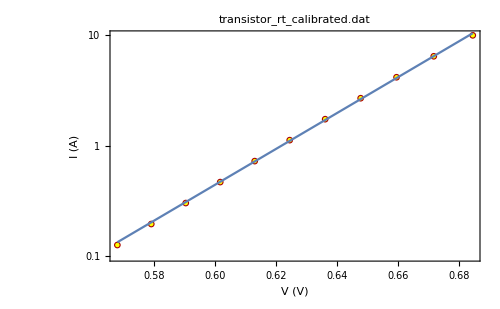
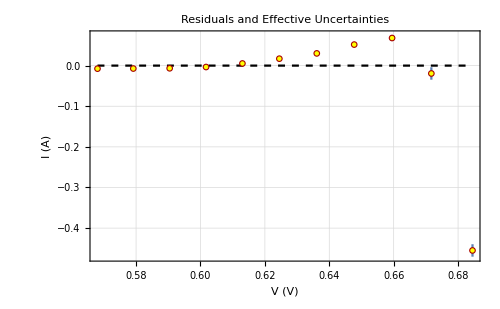
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
7.5261×10^-11 | b= 
37.4882 | 
σ_a= 
8.96097×10^-13 | σ_b= 
0.0185673 | χ^2/(n-2)= 
222.001

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.5629000000000001,0.6938548958333333},222.0012998180222];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
transistorRT=fitParam;
```

```mathematica
fitParam={};
```

### Transistor - Dry Ice Temperature

#### Whole dataset (bad points removed)

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_di.dat

File comment header:

Transistor Dry Ice calibrated
IV Data Set #00220	4:27:49 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.564039,0.881428}

n= 36

0 points removed.

```mathematica
DiodeFit[]
```

n = 36

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
2.81688×10^-21 | b= 
56.7388 | 
σ_a= 
2.32111×10^-18 | σ_b= 
0.0952952 | Std. deviation= 
0.090745

Fit of (x±σ_x,y±σ_y)

Minimizing Chi^2

a= 
1.11695×10^-21 | b= 
57.8879 | 
σ_a= 
7.44262×10^-24 | σ_b= 
0.00787585 | χ^2/(n-2)= 
578.877

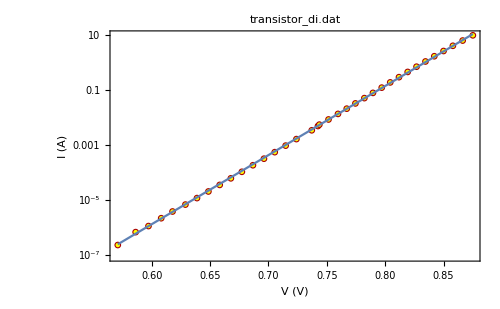
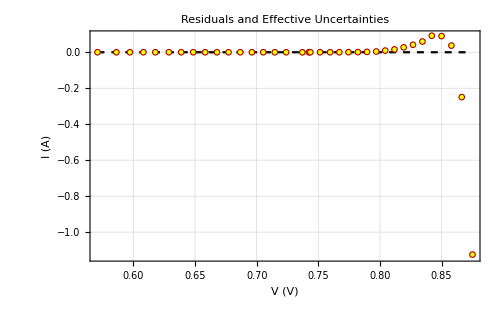
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
1.11695×10^-21 | b= 
57.8879 | 
σ_a= 
7.44262×10^-24 | σ_b= 
0.00787585 | χ^2/(n-2)= 
578.877

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.5640392291666667,0.8814277708333333},578.877313412121];
```

#### Low voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_di.dat

File comment header:

Transistor Dry Ice calibrated
IV Data Set #00220	4:27:49 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.5809,0.6621}

n= 8

28 points removed.

```mathematica
DiodeFit[]
```

n = 8

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

a= 
3.65313×10^-21 | b= 
55.9629 | 
σ_a= 
3.58819×10^-22 | σ_b= 
0.624379 | Std. deviation= 
1.08985×10^-7

Fit of (x±σ_x,y±σ_y)

Minimizing Chi^2

a= 
4.67296×10^-21 | b= 
55.578 | 
σ_a= 
5.1192×10^-22 | σ_b= 
0.163026 | χ^2/(n-2)= 
4.69663

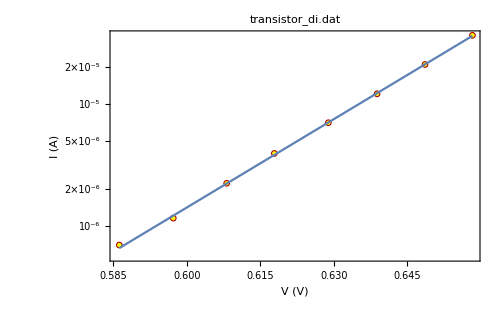
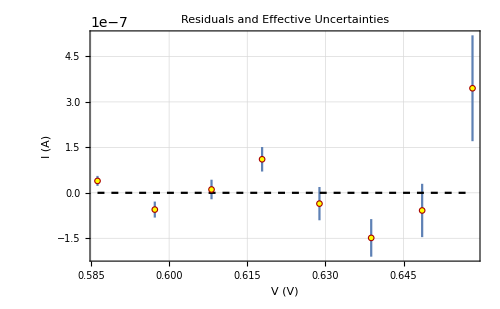
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
4.67296×10^-21 | b= 
55.578 | 
σ_a= 
5.1192×10^-22 | σ_b= 
0.163026 | χ^2/(n-2)= 
4.69663

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.5809000000000001,0.6621},4.696633498979921];
```

#### Medium voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_di.dat

File comment header:

Transistor Dry Ice calibrated
IV Data Set #00220	4:27:49 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.6731,0.786}

n= 14

22 points removed.

```mathematica
DiodeFit[]
```

n = 14

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
6.58078×10^-22 | b= 
58.586 | 
σ_a= 
1.95641×10^-22 | σ_b= 
0.0916416 | Std. deviation= 
0.000101692

Fit of (x±σ_x,y±σ_y)

Minimizing Chi^2

a= 
4.71352×10^-22 | b= 
59.0236 | 
σ_a= 
1.28114×10^-23 | σ_b= 
0.0360829 | χ^2/(n-2)= 
27.7266

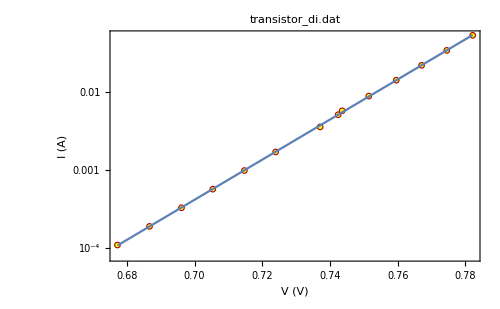
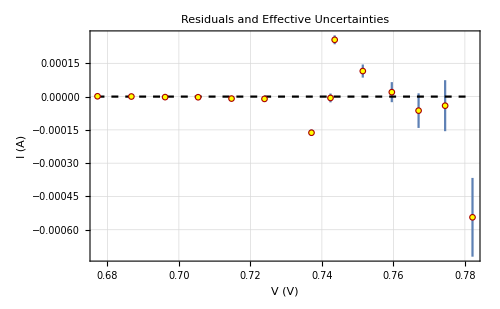
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
4.71352×10^-22 | b= 
59.0236 | 
σ_a= 
1.28114×10^-23 | σ_b= 
0.0360829 | χ^2/(n-2)= 
27.7266

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.6731,0.786},27.72657449600054];
```

#### High voltage

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 13/Diode/transistor_di.dat

File comment header:

Transistor Dry Ice calibrated
IV Data Set #00220	4:27:49 PM 5/10/2018
DAQ: PCI-6221; 16 DAC bits, -10 to 10 V; 16 ADC bits, -1.0 to 1.0 V
Sampling: samples/point 50;  settling time 8.0ms
Current calibration: Transfer resistance 0.0000Ohm; Offset 0.00V
Voltage calibration: Series resistance 0.00Ohm; Offset 0.00V
Voltage (V)    	Current (mA)     	sig I (mA)       	sig Voltage (V)

Read 40 data points.

```mathematica
NRangeRemove/@{1,1,17,17};
```

n= 39

1 point removed.

n= 38

1 point removed.

n= 37

1 point removed.

n= 36

1 point removed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.7782,0.881428}

n= 13

23 points removed.

```mathematica
DiodeFit[]
```

n = 13

y(x) = a ( Exp[b x] - 1 )

Fit of (x,y)  (unweighted)

Minimizing Chi^2

a= 
1.32598×10^-20 | b= 
54.9631 | 
σ_a= 
6.2689×10^-19 | σ_b= 
0.161531 | Std. deviation= 
0.104022

Fit of (x±σ_x,y±σ_y)

Minimizing Chi^2

a= 
6.48147×10^-21 | b= 
55.8177 | 
σ_a= 
4.3966×10^-23 | σ_b= 
0.15547 | χ^2/(n-2)= 
702.496

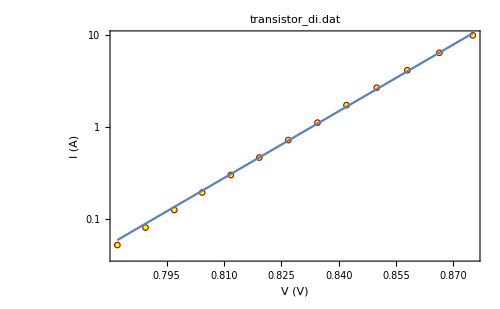
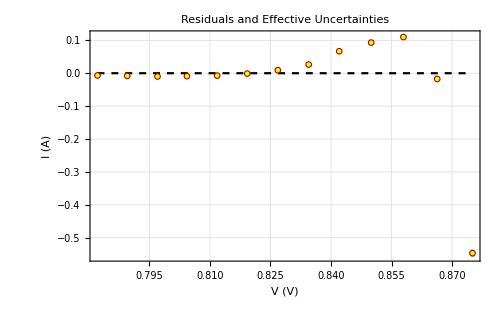
-Graphics-
-Graphics-
y(x) = a ( Exp[b x] - 1 )
a= 
6.48147×10^-21 | b= 
55.8177 | 
σ_a= 
4.3966×10^-23 | σ_b= 
0.15547 | χ^2/(n-2)= 
702.496

```mathematica
LogDifferencePlot[FrameLabel->{"V (V)","I (A)"}]
```

```mathematica
commitFit[{0.7782,0.8814277708333333},702.4964280713867];
```

```mathematica
(* We store the collected data in a separate dataset for silicon diode at room temp and re-initialize fitParam for further use. *)
transistorDI=fitParam;
```

```mathematica
fitParam={};
```

### Exporting fit data for safekeeping

```mathematica
paramList={"siliconRT","siliconDI","germaniumRT","germaniumDI","transistorRT","transistorDI"};
```

```mathematica
Export[StringJoin[#,".m"],ToExpression[#]]&/@paramList;
```

### Processing fit parameter data

```mathematica
(* We construct a list of diode parameters (η and Subscript[I, R]) from the fit parameter list for each diode configuration. This list has structure {region, Subscript[I, R],Subscript[sigI, R],η,sigη,(χ̃)^2}. *)
qe=1.6021766*10^-19 (* C *);
kb=1.3806485*10^-23 (* J K^-1 *);
t=298 (* K *);
processed[dataset_]:=Table[{dataset[[i]][[1]],10^-3 dataset[[i]][[2]],10^-3 dataset[[i]][[3]],qe/(kb t dataset[[i]][[4]]),(qe dataset[[i]][[5]])/(kb t (dataset[[i]][[4]])^2),dataset[[i]][[6]]},{i,1,Length[dataset]}];
present[dataset_,x_]:=Table[{NumberForm[dataset[[i]][[1]],4],NumberForm[10^x dataset[[i]][[2]],{8,-RealDigits[10^x dataset[[i]][[3]]][[2]]+2}],NumberForm[10^x dataset[[i]][[3]],{8,-RealDigits[10^x dataset[[i]][[3]]][[2]]+2}],NumberForm[dataset[[i]][[4]],{8,-RealDigits[dataset[[i]][[5]]][[2]]+2}],NumberForm[dataset[[i]][[5]],{8,-RealDigits[dataset[[i]][[5]]][[2]]+2}],Round[dataset[[i]][[6]]]},{i,1,Length[dataset]}];
```

```mathematica
ClearAll["siliconRT2","siliconDI2","germaniumRT2","germaniumDI2","transistorRT2","transistorDI2"];
```

```mathematica
For[i=1,i≤Length[paramList],i++,Evaluate[Symbol[StringJoin[paramList[[i]],"2"]]]=processed[ToExpression[paramList[[i]]]]];
```

```mathematica
siliconRTpresent=Join[{{"Voltage Range (V)","I_R (μA)","σ_I_R (nA)","η","σ_η","(χ̃)^2"}},present[siliconRT2,9]];
```

```mathematica
siliconDIpresent=Join[{{"Voltage Range (V)","I_R (pA)","σ_I_R (fA)","η","σ_η","(χ̃)^2"}},present[siliconDI2,15]];
```

```mathematica
germaniumRTpresent=Join[{{"Voltage Range (V)","I_R (mA)","σ_I_R (μA)","η","σ_η","(χ̃)^2"}},present[germaniumRT2,6]];
```

```mathematica
germaniumDIpresent=Join[{{"Voltage Range (V)","I_R (nA)","σ_I_R (pA)","η","σ_η","(χ̃)^2"}},present[germaniumDI2,12]];
```

```mathematica
transistorRTpresent=Join[{{"Voltage Range (V)","I_R (pA)","σ_I_R (fA)","η","σ_η","(χ̃)^2"}},present[transistorRT2,15]];
```

```mathematica
transistorDIpresent=Join[{{"Voltage Range (V)","I_R (yA)","σ_I_R (zA)","η","σ_η","(χ̃)^2"}},present[transistorDI2,24]];
```

### Processed parameter data

```mathematica
grid[data_]:=Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}];
```

#### Silicon Diode - Room temperature

```mathematica
grid[siliconRTpresent]
```

Voltage Range (V) | I_R (μA) | σ_I_R (nA) | η | σ_η | (χ̃)^2
{-0.01543,0.756} | 4.3550 | 0.0047 | 1.95420 | 0.00018 | 513
{-0.01543,0.1484} | 3.560 | 0.022 | 1.8069 | 0.0046 | 170
{0.206,0.5024} | 3.999 | 0.015 | 1.93658 | 0.00098 | 41
{0.501,0.756} | 6.564 | 0.029 | 2.01676 | 0.00071 | 626

#### Silicon Diode - Dry ice temperature

```mathematica
grid[siliconDIpresent]
```

Voltage Range (V) | I_R (pA) | σ_I_R (fA) | η | σ_η | (χ̃)^2
{0.3231,0.9117} | 14.030 | 0.036 | 1.27954 | 0.00014 | 453
{0.3231,0.5102} | 5.304 | 0.089 | 1.1961 | 0.0014 | 93
{0.5082,0.7202} | 21.94 | 0.22 | 1.30992 | 0.00070 | 22
{0.7176,0.9119} | 11.92 | 0.12 | 1.27156 | 0.00051 | 785

#### Germanium Diode - Room temperature

```mathematica
grid[germaniumRTpresent]
```

Voltage Range (V) | I_R (mA) | σ_I_R (μA) | η | σ_η | (χ̃)^2
{-0.008776,0.4179} | 4.0369 | 0.0058 | 1.98973 | 0.00045 | 10171
{-0.008776,0.0908} | 0.7776 | 0.0072 | 1.2841 | 0.0053 | 16
{0.104,0.2466} | 1.8845 | 0.0075 | 1.6624 | 0.0015 | 412
{0.2473,0.4179} | 9.782 | 0.021 | 2.28325 | 0.00080 | 4169

#### Germanium Diode - Dry ice temperature

```mathematica
grid[germaniumDIpresent]
```

Voltage Range (V) | I_R (nA) | σ_I_R (pA) | η | σ_η | (χ̃)^2
{0.0528,0.5649} | 475.9 | 1.2 | 1.23581 | 0.00022 | 43187
{0.0528,0.1999} | 20.85 | 0.50 | 0.9420 | 0.0032 | 5
{0.2008,0.3901} | 66.20 | 0.36 | 1.06489 | 0.00048 | 140
{0.4148,0.5649} | 10850. | 30. | 1.55183 | 0.00035 | 45694

#### Transistor - Room temperature

```mathematica
grid[transistorRTpresent]
```

Voltage Range (V) | I_R (pA) | σ_I_R (fA) | η | σ_η | (χ̃)^2
{0.227,0.6939} | 36.42 | 0.12 | 1.00817 | 0.00014 | 205
{0.227,0.3649} | 27.86 | 0.66 | 0.9892 | 0.0018 | 87
{0.3976,0.5514} | 30.40 | 0.43 | 0.99852 | 0.00075 | 21
{0.5629,0.6939} | 75.26 | 0.90 | 1.03876 | 0.00051 | 222

#### Transistor - Dry ice temperature

```mathematica
grid[transistorDIpresent]
```

Voltage Range (V) | I_R (yA) | σ_I_R (zA) | η | σ_η | (χ̃)^2
{0.564,0.8814} | 1.1170 | 0.0074 | 0.672703 | 0.000092 | 579
{0.5809,0.6621} | 4.67 | 0.51 | 0.7007 | 0.0021 | 5
{0.6731,0.786} | 0.471 | 0.013 | 0.65976 | 0.00040 | 28
{0.7782,0.8814} | 6.481 | 0.044 | 0.6977 | 0.0019 | 702

### Analysis of the PN junction theory

#### Fit residuals

We observe that our fits share the same structure in the fit residuals, indicating that the PN junction theory presented does not completely explain the I-V behavior of PN-junction diodes. This structure is easy to observe in the plots above: residuals start out small, then increase in the positive direction (positive residuals increasing in magnitude), then decrease in magnitude, cross the zero-residual line, and dramatically increase in the negative direction (negative residuals increasing in magnitude). This indicates either that our theory must contain a correction term we have not accounted for, and/or our assumption that the ideality coefficient η is a constant over a given I-V curve in fact does not adequately hold over our measured regions.

#### Residuals over different regions

Following the observations above, we attempted several fits for each dataset - for each diode at both temperature (room temperature and dry ice temperature), we perform a fit over low-current, medium-current, and high-current regions. From the fit parameters, we can obtain I_R and η, the results of which are shown in the tables above for all diodes, temperatures, and current regions, along with the corresponding (χ̃)^2 of the fit.

We observe that the residuals maintain the general structure described above over all fitted regions.  Furthermore, we observe a significant variation in goodness-of-fit ((χ̃)^2) over different regions of the same IV-curve. This indicates that there must be a correction term to our model, and that this correction term cannot present itself only as a variation in η across the IV-curve (if it were only a variation in η, we would expect the goodness-of-fit of our data to the model to always improve when we fit over smaller subsections of our data, and this is not consistently observed in the tables above for the high-current fits, indicating the presence of a correction term not in η that becomes significant at high currents). However, the significant differences in (χ̂)^2 and in our best estimates for η using the fits over subsections of each IV-curve indicate that the correction term does include a variation of η over the IV-curve.

#### Observations from fits

The different diodes differ in their behavior over different current and temperature ranges. The best fits are obtained using the germanium diode and the transistor at dry ice temperatures, over the low current range. The germanium diode at dry ice temperature seems to fit the model relatively well when fit over subsections of the IV-curve, but has a much worse fit over the entire dataset. This indicates that η is not approximately constant as assumed for this configuration, and that the correction term to the model is dominated by the variation of η across the IV-curve for this configuration. The transistor at dry ice temperature has the same issue, but much less severe. It is therefore the dataset that fits the model the most closely. The transistor at room temperature fits the model best over the whole dataset, but it is not a very good fit ((χ̃)^2=205).

With the exception of the silicon diode at both temperatures and the transistor at room temperature, we observe that the data fits the model best at low-current, worsening as current increases. This general trend may be caused by series resistance becoming apparent at high-currents.

## Series resistance

At large currents, we expect a voltage drop to occur due to the resistance between each of the diode’s connecting leads. This causes a current-dependent decrease in the voltage across the diode, such that at high currents the IV-curve for the diode diverges from and lies below the IV-curve predicted by the theory, with divergence from the theory increasing with current. Now, recall that the diode equation predicts current across the diode to vary exponentially with the inverse of temperature, T. Therefore, assuming resistance changes only slowly with temperature, we expect larger currents at lower temperatures for a given voltage to result in series resistance to have a greater effect on the cold data than on the room temperature data.

Below is an interactive plot where we can observe the effects of series resistance on the IV-curves predicted by the theory, for a diode with I_R=10^-9 A and η = 1. We obtain the plot by numerically solving the implicit equation resulting from applying Kirchoff’s Voltage Law to a voltage drop across a diode in series with a resistor, whose resistance can be varied to observe the effects on the IV-curves.

```mathematica
ClearAll[t,i]
```

```mathematica
iR=10^-9;
eta=1;
```

```mathematica
i[ir_,η_,v_,t_]:=ir(ⅇ^((qe v)/(η kb t))-1);
```

```mathematica
iRes[ir_,η_,v_,t_,r_]:=i[ir,η,vDiode,t]/.FindRoot[v==i[ir,η,vDiode,t] r+vDiode,{vDiode,v}][[1]]//Quiet
```

```mathematica
Manipulate[LogPlot[{iRes[iR,eta,v,298,r],iRes[iR,eta,v,194,r],i[iR,eta,v,298],i[iR,eta,v,194]},{v,0,0.8},FrameLabel->{"V (V)","I (A)"},PlotLegends->{"With series resistance 
(Room Temperature)","With series resistance 
(Dry Ice)","Without series resistance 
(Room Temperature)","Without series resistance 
(Dry Ice)"},PlotRange->All,ImageSize->400,LabelStyle->{FontSize->10}],{{r,0,"Series Resistance (Ω)"},0,0.2}]
```

Indeed, in the plot above, we can observe a series resistance effect with the characteristics proposed above at high currents, with a greater effect on the cold IV-curve than on the room temperature IV-curve (the onset of significant divergence from the diode equation occurs at lower voltages in the cold IV-curve).

Now, observe that the data from the fits presented above shows significantly worse fits for high-current data, with the high-current fits worsening at dry-ice temperature. From the above, this is exactly what we would expect of data containing evidence of series resistance being fit against the diode equation. This indicates that the correction terms to our diode equation must account for series resistance, and as stated before, variability of η across the IV-curve.

## Determining E_g

Solving equation (13.2) from the lab manual for two different temperatures T_1, T_2, we obtain an expression of for E_g in units of eV:

E_g=k_B/q_e((η_1 η_2)(T_1 T_2))/(T_2 η_2 - T_1 η_1)Log[I_R_1/I_R_2].

```mathematica
<<SimpleErrorPropagation`
```

```mathematica
?PropagateUncertainties
```

PropagateUncertainties[func, vars] propagates uncertainties in variables listed in vars = {variable1, variable2,...} and retuns the propagated uncertainty in func.
func must necessarily be differentiable with respect to all variables in vars, and the uncertainties in variables in vars must be independent.

It will return an algebraic expression in terms of the variables in vars, with uncertainty in some variable denoted by sigmaVariable.
It can be used either by providing an algebraic expression, then substituting values for the variables and uncertainties in a subsequent operation, or simply by assigning values and uncertainties to each variable using the naming conventions mentioned. In the latter case, it will be necessary to localize the variables in vars using Module or Block.

Note: Loading SimpleErrorPropagation` clears any variables named 'variance', 'varianceList' or 'PropagateUncertainties' due to function and subfunction names in the Package.

```mathematica
eg[t1_,t2_,ir1_,ir2_,eta1_,eta2_]:=kb/qe((eta1 eta2)(t1 t2))/(t2 eta2 - t1 eta1)Log[ir2/ir1];
```

```mathematica
PropagateUncertainties[eg[t1,t2,ir1,ir2,eta1,eta2],{eta1,eta2,ir1,ir2}]//Simplify
```

√(1/(ir1^2 ir2^2 (eta1 t1-1. eta2 t2)^4)t1^2 t2^2 (eta1^2 eta2^2 (eta1^2 (7.42584×10^-9 ir2^2 sigmaIr1^2+7.42584×10^-9 ir1^2 sigmaIr2^2) t1^2+eta1 eta2 (-1.48517×10^-8 ir2^2 sigmaIr1^2-1.48517×10^-8 ir1^2 sigmaIr2^2) t1 t2+eta2^2 (7.42584×10^-9 ir2^2 sigmaIr1^2+7.42584×10^-9 ir1^2 sigmaIr2^2) t2^2)+ir1^2 ir2^2 (7.42584×10^-9 eta1^4 sigmaEta2^2 t1^2+7.42584×10^-9 eta2^4 sigmaEta1^2 t2^2) Log[ir2/ir1]^2))

```mathematica
egUnc[t1_,t2_,ir1_,sigmaIr1_,ir2_,sigmaIr2_,eta1_,sigmaEta1_,eta2_,sigmaEta2_]:={eg[t1,t2,ir1,ir2,eta1,eta2],√(1/(ir1^2 ir2^2 (eta1 t1-1. eta2 t2)^4)t1^2 t2^2 (eta1^2 eta2^2 (eta1^2 (7.425838191741328*^-9 ir2^2 sigmaIr1^2+7.425838191741328*^-9 ir1^2 sigmaIr2^2) t1^2+eta1 eta2 (-1.4851676383482656*^-8 ir2^2 sigmaIr1^2-1.4851676383482656*^-8 ir1^2 sigmaIr2^2) t1 t2+eta2^2 (7.425838191741328*^-9 ir2^2 sigmaIr1^2+7.425838191741328*^-9 ir1^2 sigmaIr2^2) t2^2)+ir1^2 ir2^2 (7.425838191741328*^-9 eta1^4 sigmaEta2^2 t1^2+7.425838191741328*^-9 eta2^4 sigmaEta1^2 t2^2) Log[ir2/ir1]^2))};
```

```mathematica
diodeList={"siliconRT2","siliconDI2","germaniumRT2","germaniumDI2","transistorRT2","transistorDI2"};
```

```mathematica
(* List of best fit estimates of diode parameters, ordered as given by diodeList above. *)
```

```mathematica
bestFits=Flatten[
Table[
Select[
Evaluate[
Symbol[
diodeList[[i]]]],
#[[6]]==Min[
Evaluate[
Symbol[
diodeList[[i]]]][[All,6]]]
&],
{i,1,Length[diodeList]}],1
];
```

```mathematica
egList=Table[egUnc[298,194.67,bestFits[[2 i-1]][[2]],bestFits[[2 i-1]][[3]],bestFits[[2 i]][[2]],bestFits[[2 i]][[3]],bestFits[[2 i-1]][[4]],bestFits[[2 i-1]][[5]],bestFits[[2 i]][[4]],bestFits[[2 i]][[5]]],{i,1,Length[bestFits]/2}];
```

```mathematica
egPresent={{},{},{}};
egPresent[[1]]=Join[{"Silicon Diode"},egList[[1]]];
egPresent[[2]]=Join[{"Germanium Diode"},egList[[2]]];
egPresent[[3]]=Join[{"Transistor"},egList[[3]]];
```

```mathematica
egPresent=Join[{{"Diode Type","E_g(eV)","σ_E_g(eV)"}},egPresent];
```

```mathematica
egPresent[[2]][[2]]=NumberForm[egPresent[[2]][[2]],{8,5}];
```

```mathematica
egPresent[[2]][[3]]=NumberForm[egPresent[[2]][[3]],{8,5}];
```

```mathematica
egPresent[[3]][[2]]=NumberForm[egPresent[[3]][[2]],{8,4}];
egPresent[[3]][[3]]=NumberForm[egPresent[[3]][[3]],{8,4}];
```

```mathematica
egPresent[[4]][[2]]=NumberForm[egPresent[[4]][[2]],{8,4}];
egPresent[[4]][[3]]=NumberForm[egPresent[[4]][[3]],{8,4}];
```

```mathematica
grid[egPresent]
```

Diode Type | E_g(eV) | σ_E_g(eV)
Silicon Diode | 0.47692 | 0.00065
Germanium Diode | 0.3194 | 0.0025
Transistor | 0.4904 | 0.0036

We observe large discrepancies between our estimates above and the known semiconductor gap energies of 1.12 eV for silicon and 0.67 eV for germanium. This could be due to a variety of factors, including the stated variability of η across the IV-curve which we have neglected in our analysis, imperfections in the PN-junctions of our diode, ohmic heating in the diode, undetected systematic errors in the apparatus, or human error during calibration.

## Limitations of diode equation

The idealized one-dimensional model of the diode neglects effects such as internal resistance of the diode, capacitance between the two sides of the depletion layer, band gap shift due to doping.